## Planck Constraints

```mathematica
(*Import the CSV file with semicolon-separated values*)data=Import[FileNameJoin[{NotebookDirectory[],"PLANCK Data.csv"}],"Table","FieldSeparators"->{";"}];
(*Separate headers and values*)
data=Rest[data];
headers=First[data];
values=Rest[data];
(*create a dataset with headers*)
dataset=Dataset[AssociationThread[headers->#]&/@values];
(*Preview the dataset*)
dataset;
```

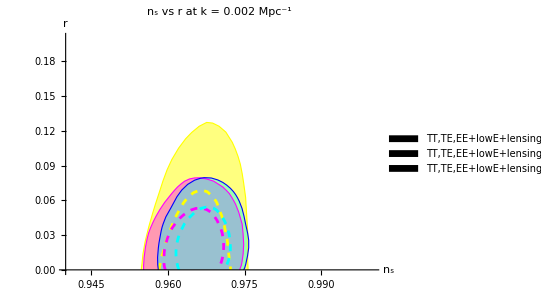

```mathematica
(*Create a ListPlot*)
Observations=ListLinePlot[{
Transpose[{dataset[All,"ns95"]//Normal//ToExpression,dataset[All,"r95"]//Normal//ToExpression}],
Transpose[{dataset[All,"nsBK95"]//Normal//ToExpression,dataset[All,"rBK95"]//Normal//ToExpression}],
Transpose[{dataset[All,"nsBAO95"]//Normal//ToExpression,dataset[All,"rBAO95"]//Normal//ToExpression}],
Transpose[{dataset[All,"ns65"]//Normal//ToExpression,dataset[All,"r65"]//Normal//ToExpression}],
Transpose[{dataset[All,"nsBK68"]//Normal//ToExpression,dataset[All,"rBK68"]//Normal//ToExpression}],
Transpose[{dataset[All,"nsBAO68"]//Normal//ToExpression,dataset[All,"rBAO68"]//Normal//ToExpression}]},
PlotRange->{{0.94,1},{0,0.2}},
AxesLabel->{"n_s","r"},PlotLabel->"n_s vs r at k = 0.002 Mpc^-1",
GridLines->None,
AspectRatio->0.75,
PlotStyle->{
{Yellow,Thickness[0.005],Dashed},
{Magenta,Thickness[0.005],Dashed},
{Cyan,Thickness[0.005],Dashed},
{Yellow,Thickness[0.002]},
{Magenta,Thickness[0.002]},
{Blue,Thickness[0.002]}},
Filling->{4->Axis,5->Axis,6->Axis,1->Axis,2->Axis,3->Axis},
FillingStyle->
{1->Directive[Yellow,Opacity[0]],
2->Directive[Magenta,Opacity[0]],
3->Directive[Cyan,Opacity[0]],
4->Directive[Yellow,Opacity[0.5]],
5->Directive[Magenta,Opacity[0.4]],
6->Directive[Cyan,Opacity[0.4]]},
PlotLegends->Placed[SwatchLegend[{
Style["TT,TE,EE+lowE+lensing",Small],
Style["TT,TE,EE+lowE+lensing+BK14",Small],Style["TT,TE,EE+lowE+lensing+BK14+BAO",Small]},LegendMarkers->Graphics[Rectangle[]],
LegendFunction->"Frame"],Right]]
```

## Your Plot

```mathematica
(* Express your ns and r in terms of N *)
```

```mathematica
ns[Ne_]=1-2/Ne-3/Ne^2 ;
r[Ne_]=12/Ne^2 ;
Nmin=50;
Nmax=60;
(* Parametric plot *)
yourModel=ParametricPlot[{ns[Ne],r[Ne]},{Ne,Nmin,Nmax},PlotRange->{{0.94,1},{0,0.2}},
AspectRatio->0.75,
PlotStyle->{Blue,Thickness[0.015]},
PlotLegends->Placed[SwatchLegend[{
Style["Starobinsky Inflation"]},LegendMarkers->"Line",
LegendFunction->"Frame"],Right]];
```

```mathematica
(* If you know "r vs ns" relation for your model *)
rr[nss_]=8(1-nss) ;
(* Curve plot *)
yourCurve=Plot[rr[nss],{nss,0.94,1},PlotStyle->{Green,Thickness[0.003]},
PlotLegends->Placed[SwatchLegend[{
Style["Power Law Potential"]},LegendMarkers->"Line",
LegendFunction->"Frame"],Right]];
```

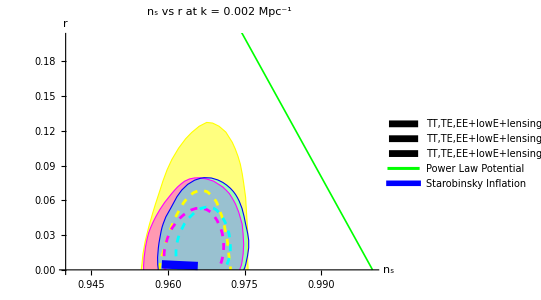

```mathematica
finalPlot=Show[Observations,yourCurve,yourModel]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"plot.pdf"}],finalPlot]
```